## Numerical Example Ambartsumyan et al. CMAME (2020) :

### Displacement :

```mathematica
u[x_,y_,t_]:=Exp[t]{x^3 y^4+x^2+Sin[(1-x)(1-y)]Cos[1-y],(1-x)^4(1-y)^3+(1-y)^2+Cos[x y]Sin[x]}
```

Dirichlet boundary conditions : (they are not homogeneous)

```mathematica
u[0,y,t]
```

{ⅇ^t Cos[1-y] Sin[1-y],ⅇ^t ((1-y)^2+(1-y)^3)}

```mathematica
u[1,y,t]
```

{ⅇ^t (1+y^4),ⅇ^t ((1-y)^2+Cos[y] Sin[1])}

```mathematica
u[x,0,t]
```

{ⅇ^t (x^2+Cos[1] Sin[1-x]),ⅇ^t (1+(1-x)^4+Sin[x])}

```mathematica
u[x,1,t]
```

{ⅇ^t (x^2+x^3),ⅇ^t Cos[x] Sin[x]}

ContourPlot of the Magnitude of the displacement (Euclidean norm) :

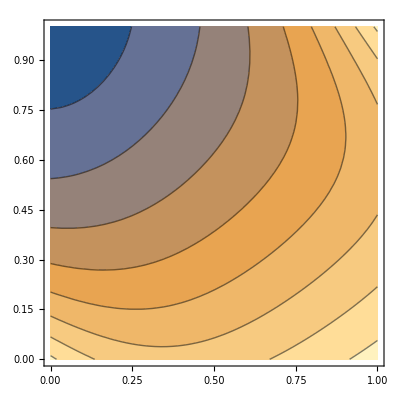

```mathematica
ContourPlot[Sqrt[(Exp[t](x^3 y^4+x^2+Sin[(1-x)(1-y)]Cos[1-y]))^2+(Exp[t]((1-x)^4(1-y)^3+(1-y)^2+Cos[x y]Sin[x]))^2]/.t->0.001,{x,0,1},{y,0,1}]
```

### Pressure:

```mathematica
p[x_,y_,t_]:=Exp[t](10+Sin[Pi x] Cos[Pi y])
```

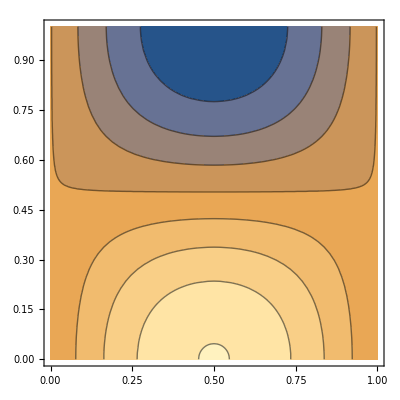

```mathematica
ContourPlot[p[x,y,0.001],{x,0,1},{y,0,1}]
```

### Elastic Stress:

```mathematica
{D[(Exp[t](x^3 y^4+x^2+Sin[(1-x)(1-y)]Cos[1-y])), x],D[(Exp[t](x^3 y^4+x^2+Sin[(1-x)(1-y)]Cos[1-y])), y]}//Simplify
```

{ⅇ^t (x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]),ⅇ^t (4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Sin[1-y] Sin[(-1+x) (-1+y)])}

```mathematica
{D[(Exp[t]((1-x)^4(1-y)^3+(1-y)^2+Cos[x y]Sin[x])), x],D[(Exp[t]((1-x)^4(1-y)^3+(1-y)^2+Cos[x y]Sin[x])), y]}//Simplify
```

{ⅇ^t (-4 (-1+x)^3 (-1+y)^3+Cos[x] Cos[x y]-y Sin[x] Sin[x y]),ⅇ^t (2 (-1+y)-3 (-1+x)^4 (-1+y)^2-x Sin[x] Sin[x y])}

```mathematica
Gradu[x_,y_,t_]:={{ⅇ^t (x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]),ⅇ^t (4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Sin[1-y] Sin[(-1+x) (-1+y)])},{ⅇ^t (-4 (-1+x)^3 (-1+y)^3+Cos[x] Cos[x y]-y Sin[x] Sin[x y]),ⅇ^t (2 (-1+y)-3 (-1+x)^4 (-1+y)^2-x Sin[x] Sin[x y])}}
```

Let us define ϵ (u) :

```mathematica
1/2*(Gradu[x,y,t]+Transpose[Gradu[x,y,t]])//Simplify
```

{{ⅇ^t (x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]),1/2 ⅇ^t (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y])},{1/2 ⅇ^t (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y]),ⅇ^t (2 (-1+y)-3 (-1+x)^4 (-1+y)^2-x Sin[x] Sin[x y])}}

```mathematica
EE[x_,y_]:=5+Sin[5 Pi x]Sin[5 Pi y];
mu[x_,y_]=EE[x,y]/(2(1+nu));
lambda[x_,y_]=EE[x,y]*nu/((1+nu)(1-2 nu));
```

Let us compute the stress σ= A^-1 ϵ(u): (Using the expression for A^-1 given in equation (3 . 2 . 9) of Ambartsumyan PhD. Thesis)

```mathematica
2 mu[x,y] {{ⅇ^t (x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]),1/2 ⅇ^t (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y])},{1/2 ⅇ^t (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y]),ⅇ^t (2 (-1+y)-3 (-1+x)^4 (-1+y)^2-x Sin[x] Sin[x y])}}+lambda[x,y] {{ⅇ^t (x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]+2 (-1+y)-3 (-1+x)^4 (-1+y)^2-x Sin[x] Sin[x y]),0},{0,ⅇ^t (x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]+2 (-1+y)-3 (-1+x)^4 (-1+y)^2-x Sin[x] Sin[x y])}}//Simplify
```

{{1/(1+nu)ⅇ^t (5+Sin[5 π x] Sin[5 π y]) (x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]+1/(1-2 nu)nu (2 (-1+y)-3 (-1+x)^4 (-1+y)^2+x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y])),1/(2 (1+nu))ⅇ^t (5+Sin[5 π x] Sin[5 π y]) (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y])},{1/(2 (1+nu))ⅇ^t (5+Sin[5 π x] Sin[5 π y]) (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y]),1/(1+nu)ⅇ^t (5+Sin[5 π x] Sin[5 π y]) (2 (-1+y)-3 (-1+x)^4 (-1+y)^2-x Sin[x] Sin[x y]+1/(1-2 nu)nu (2 (-1+y)-3 (-1+x)^4 (-1+y)^2+x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y]))}}

Let us define the stress function as the previous expression :

```mathematica
Sigmae[x_,y_,t_]:={{1/(1+nu)ⅇ^t (5+Sin[5 π x] Sin[5 π y]) (x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]+1/(1-2 nu)nu (2 (-1+y)-3 (-1+x)^4 (-1+y)^2+x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y])),1/(2 (1+nu))ⅇ^t (5+Sin[5 π x] Sin[5 π y]) (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y])},{1/(2 (1+nu))ⅇ^t (5+Sin[5 π x] Sin[5 π y]) (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y]),1/(1+nu)ⅇ^t (5+Sin[5 π x] Sin[5 π y]) (2 (-1+y)-3 (-1+x)^4 (-1+y)^2-x Sin[x] Sin[x y]+1/(1-2 nu)nu (2 (-1+y)-3 (-1+x)^4 (-1+y)^2+x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y]))}}
```

### Stress:

```mathematica
Sigmae[x,y,t]-alpha {{p[x,y,t],0},{0,p[x,y,t]}}//Simplify
```

{{ⅇ^t (-alpha (10+Cos[π y] Sin[π x])+1/(1+nu)(5+Sin[5 π x] Sin[5 π y]) (x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]+1/(1-2 nu)nu (2 (-1+y)-3 (-1+x)^4 (-1+y)^2+x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y]))),1/(2 (1+nu))ⅇ^t (5+Sin[5 π x] Sin[5 π y]) (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y])},{1/(2 (1+nu))ⅇ^t (5+Sin[5 π x] Sin[5 π y]) (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y]),ⅇ^t (-alpha (10+Cos[π y] Sin[π x])+1/(1+nu)(5+Sin[5 π x] Sin[5 π y]) (2 (-1+y)-3 (-1+x)^4 (-1+y)^2-x Sin[x] Sin[x y]+1/(1-2 nu)nu (2 (-1+y)-3 (-1+x)^4 (-1+y)^2+x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y])))}}

```mathematica
Sigma[x_,y_,t_]:={{ⅇ^t (-alpha (10+Cos[π y] Sin[π x])+1/(1+nu)(5+Sin[5 π x] Sin[5 π y]) (x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]+1/(1-2 nu)nu (2 (-1+y)-3 (-1+x)^4 (-1+y)^2+x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y]))),1/(2 (1+nu))ⅇ^t (5+Sin[5 π x] Sin[5 π y]) (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y])},{1/(2 (1+nu))ⅇ^t (5+Sin[5 π x] Sin[5 π y]) (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y]),ⅇ^t (-alpha (10+Cos[π y] Sin[π x])+1/(1+nu)(5+Sin[5 π x] Sin[5 π y]) (2 (-1+y)-3 (-1+x)^4 (-1+y)^2-x Sin[x] Sin[x y]+1/(1-2 nu)nu (2 (-1+y)-3 (-1+x)^4 (-1+y)^2+x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y])))}}
```

ContourPlot of the Magnitude of the first row of σ :

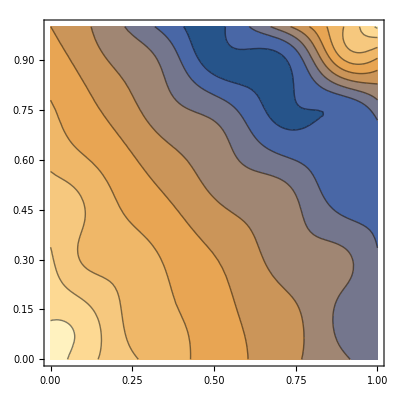

```mathematica
ContourPlot[Sqrt[(ⅇ^t (-alpha (10+Cos[π y] Sin[π x])+1/(1+nu)(5+Sin[5 π x] Sin[5 π y]) (x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]+1/(1-2 nu)nu (2 (-1+y)-3 (-1+x)^4 (-1+y)^2+x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y]))))^2+(1/(2 (1+nu))ⅇ^t (5+Sin[5 π x] Sin[5 π y]) (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y]))^2]/.{t->0.001,nu->0.2,alpha->1},{x,0,1},{y,0,1}]
```

ContourPlot of the Magnitude of the second row of σ :

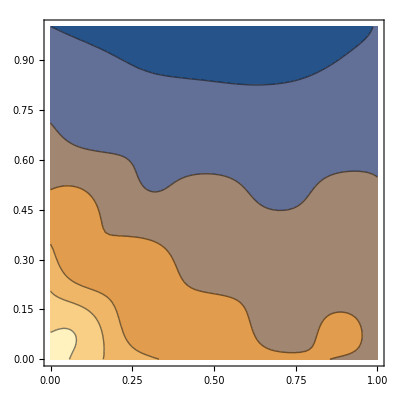

```mathematica
ContourPlot[Sqrt[(1/(2 (1+nu))ⅇ^t (5+Sin[5 π x] Sin[5 π y]) (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y]))^2+(ⅇ^t (-alpha (10+Cos[π y] Sin[π x])+1/(1+nu)(5+Sin[5 π x] Sin[5 π y]) (2 (-1+y)-3 (-1+x)^4 (-1+y)^2-x Sin[x] Sin[x y]+1/(1-2 nu)nu (2 (-1+y)-3 (-1+x)^4 (-1+y)^2+x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y]))))^2]/.{t->0.001,nu->0.2,alpha->1},{x,0,1},{y,0,1}]
```

### Rotation :

```mathematica
1/2*(Gradu[x,y,t]-Transpose[Gradu[x,y,t]])//Simplify
```

{{0,1/2 ⅇ^t (4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]-Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]+y Sin[x] Sin[x y])},{1/2 ⅇ^t (-4 (-1+x)^3 (-1+y)^3-4 x^3 y^3-(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]-Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y]),0}}

ContourPlot of the element in the first row and second column of the rotation:

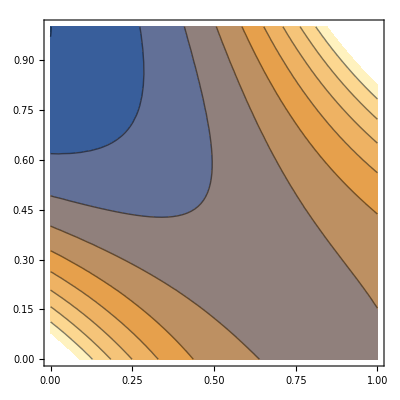

```mathematica
ContourPlot[1/2 ⅇ^t (4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]-Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]+y Sin[x] Sin[x y])/.t->0.001,{x,0,1},{y,0,1}]
```

### Darcy velocity :

```mathematica
KK[x_,y_]:={{(x+1)^2+y^2, Sin[x y]},{Sin[x y], (x+1)^2}}
```

```mathematica
-KK[x,y].{D[p[x,y,t],x],D[p[x,y,t],y]}//Simplify
```

{ⅇ^t π (-(((1+x)^2+y^2) Cos[π x] Cos[π y])+Sin[π x] Sin[π y] Sin[x y]),ⅇ^t π ((1+x)^2 Sin[π x] Sin[π y]-Cos[π x] Cos[π y] Sin[x y])}

```mathematica
z[x_,y_,t_]:={ⅇ^t π (-(((1+x)^2+y^2) Cos[π x] Cos[π y])+Sin[π x] Sin[π y] Sin[x y]),ⅇ^t π ((1+x)^2 Sin[π x] Sin[π y]-Cos[π x] Cos[π y] Sin[x y])}
```

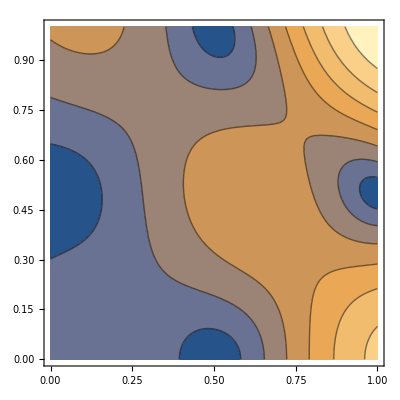

```mathematica
ContourPlot[Sqrt[(ⅇ^t π (-(((1+x)^2+y^2) Cos[π x] Cos[π y])+Sin[π x] Sin[π y] Sin[x y]))^2+(ⅇ^t π ((1+x)^2 Sin[π x] Sin[π y]-Cos[π x] Cos[π y] Sin[x y]))^2]/.{t->0.001},{x,0,1},{y,0,1}]
```

### Source term f :

```mathematica
Sigma[x,y,t]
```

{{ⅇ^t (-alpha (10+Cos[π y] Sin[π x])+1/(1+nu)(5+Sin[5 π x] Sin[5 π y]) (x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]+1/(1-2 nu)nu (2 (-1+y)-3 (-1+x)^4 (-1+y)^2+x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y]))),1/(2 (1+nu))ⅇ^t (5+Sin[5 π x] Sin[5 π y]) (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y])},{1/(2 (1+nu))ⅇ^t (5+Sin[5 π x] Sin[5 π y]) (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y]),ⅇ^t (-alpha (10+Cos[π y] Sin[π x])+1/(1+nu)(5+Sin[5 π x] Sin[5 π y]) (2 (-1+y)-3 (-1+x)^4 (-1+y)^2-x Sin[x] Sin[x y]+1/(1-2 nu)nu (2 (-1+y)-3 (-1+x)^4 (-1+y)^2+x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y])))}}

f1

```mathematica
-(D[ⅇ^t (-alpha (10+Cos[π y] Sin[π x])+1/(1+nu)(5+Sin[5 π x] Sin[5 π y]) (x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]+1/(1-2 nu)nu (2 (-1+y)-3 (-1+x)^4 (-1+y)^2+x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y]))),x]+D[1/(2 (1+nu))ⅇ^t (5+Sin[5 π x] Sin[5 π y]) (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y]),y])//Simplify
```

1/2 ⅇ^t (-1/(1+nu)(5+Sin[5 π x] Sin[5 π y]) (-12 (-1+x)^3 (-1+y)^2+12 x^3 y^2-x y Cos[x y] Sin[x]+2 (-1+x) Cos[(-1+x) (-1+y)] Sin[1-y]-Cos[1-y] Sin[(-1+x) (-1+y)]-(-1+x)^2 Cos[1-y] Sin[(-1+x) (-1+y)]-x Cos[x] Sin[x y]-Sin[x] Sin[x y])-1/(1+nu)5 π Cos[5 π y] Sin[5 π x] (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y])-2 (-alpha π Cos[π x] Cos[π y]+1/(1+nu)(5+Sin[5 π x] Sin[5 π y]) (2+6 x y^4-(-1+y)^2 Cos[1-y] Sin[(-1+x) (-1+y)]+1/(1-2 nu)nu (2-12 (-1+x)^3 (-1+y)^2+6 x y^4-x y Cos[x y] Sin[x]-(-1+y)^2 Cos[1-y] Sin[(-1+x) (-1+y)]-x Cos[x] Sin[x y]-Sin[x] Sin[x y]))+1/(1+nu)5 π Cos[5 π x] Sin[5 π y] (x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]+1/(1-2 nu)nu (2 (-1+y)-3 (-1+x)^4 (-1+y)^2+x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y]))))

```mathematica
f1[x_,y_,t_]:=1/2 ⅇ^t (-1/(1+nu)(5+Sin[5 π x] Sin[5 π y]) (-12 (-1+x)^3 (-1+y)^2+12 x^3 y^2-x y Cos[x y] Sin[x]+2 (-1+x) Cos[(-1+x) (-1+y)] Sin[1-y]-Cos[1-y] Sin[(-1+x) (-1+y)]-(-1+x)^2 Cos[1-y] Sin[(-1+x) (-1+y)]-x Cos[x] Sin[x y]-Sin[x] Sin[x y])-1/(1+nu)5 π Cos[5 π y] Sin[5 π x] (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y])-2 (-alpha π Cos[π x] Cos[π y]+1/(1+nu)(5+Sin[5 π x] Sin[5 π y]) (2+6 x y^4-(-1+y)^2 Cos[1-y] Sin[(-1+x) (-1+y)]+1/(1-2 nu)nu (2-12 (-1+x)^3 (-1+y)^2+6 x y^4-x y Cos[x y] Sin[x]-(-1+y)^2 Cos[1-y] Sin[(-1+x) (-1+y)]-x Cos[x] Sin[x y]-Sin[x] Sin[x y]))+1/(1+nu)5 π Cos[5 π x] Sin[5 π y] (x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]+1/(1-2 nu)nu (2 (-1+y)-3 (-1+x)^4 (-1+y)^2+x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y]))))
```

f2

```mathematica
-(D[1/(2 (1+nu))ⅇ^t (5+Sin[5 π x] Sin[5 π y]) (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y]),x]+D[ⅇ^t (-alpha (10+Cos[π y] Sin[π x])+1/(1+nu)(5+Sin[5 π x] Sin[5 π y]) (2 (-1+y)-3 (-1+x)^4 (-1+y)^2-x Sin[x] Sin[x y]+1/(1-2 nu)nu (2 (-1+y)-3 (-1+x)^4 (-1+y)^2+x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y]))),y])//Simplify
```

1/2 ⅇ^t (-1/(1+nu)(5+Sin[5 π x] Sin[5 π y]) (-12 (-1+x)^2 (-1+y)^3+12 x^2 y^3+Cos[1-y] Cos[(-1+x) (-1+y)]-Cos[x y] Sin[x]-y^2 Cos[x y] Sin[x]+(-1+y) Cos[(-1+x) (-1+y)] Sin[1-y]-(-1+x) (-1+y) Cos[1-y] Sin[(-1+x) (-1+y)]-2 y Cos[x] Sin[x y])-1/(1+nu)5 π Cos[5 π x] Sin[5 π y] (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y])-2 (alpha π Sin[π x] Sin[π y]+1/(1+nu)(2-6 (-1+x)^4 (-1+y)-x^2 Cos[x y] Sin[x]+1/(1-2 nu)nu (2-6 (-1+x)^4 (-1+y)+12 x^2 y^3+Cos[1-y] Cos[(-1+x) (-1+y)]-x^2 Cos[x y] Sin[x]+(-1+y) Cos[(-1+x) (-1+y)] Sin[1-y]-(-1+x) (-1+y) Cos[1-y] Sin[(-1+x) (-1+y)])) (5+Sin[5 π x] Sin[5 π y])+1/(1+nu)5 π Cos[5 π y] Sin[5 π x] (2 (-1+y)-3 (-1+x)^4 (-1+y)^2-x Sin[x] Sin[x y]+1/(1-2 nu)nu (2 (-1+y)-3 (-1+x)^4 (-1+y)^2+x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y]))))

```mathematica
f2[x_,y_,t_]:=1/2 ⅇ^t (-1/(1+nu)(5+Sin[5 π x] Sin[5 π y]) (-12 (-1+x)^2 (-1+y)^3+12 x^2 y^3+Cos[1-y] Cos[(-1+x) (-1+y)]-Cos[x y] Sin[x]-y^2 Cos[x y] Sin[x]+(-1+y) Cos[(-1+x) (-1+y)] Sin[1-y]-(-1+x) (-1+y) Cos[1-y] Sin[(-1+x) (-1+y)]-2 y Cos[x] Sin[x y])-1/(1+nu)5 π Cos[5 π x] Sin[5 π y] (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y])-2 (alpha π Sin[π x] Sin[π y]+1/(1+nu)(2-6 (-1+x)^4 (-1+y)-x^2 Cos[x y] Sin[x]+1/(1-2 nu)nu (2-6 (-1+x)^4 (-1+y)+12 x^2 y^3+Cos[1-y] Cos[(-1+x) (-1+y)]-x^2 Cos[x y] Sin[x]+(-1+y) Cos[(-1+x) (-1+y)] Sin[1-y]-(-1+x) (-1+y) Cos[1-y] Sin[(-1+x) (-1+y)])) (5+Sin[5 π x] Sin[5 π y])+1/(1+nu)5 π Cos[5 π y] Sin[5 π x] (2 (-1+y)-3 (-1+x)^4 (-1+y)^2-x Sin[x] Sin[x y]+1/(1-2 nu)nu (2 (-1+y)-3 (-1+x)^4 (-1+y)^2+x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y]))))
```

### Source term q :

```mathematica
u[x,y,t]
```

{ⅇ^t (x^2+x^3 y^4+Cos[1-y] Sin[(1-x) (1-y)]),ⅇ^t ((1-y)^2+(1-x)^4 (1-y)^3+Cos[x y] Sin[x])}

```mathematica
z[x,y,t]
```

{ⅇ^t π (-(((1+x)^2+y^2) Cos[π x] Cos[π y])+Sin[π x] Sin[π y] Sin[x y]),ⅇ^t π ((1+x)^2 Sin[π x] Sin[π y]-Cos[π x] Cos[π y] Sin[x y])}

```mathematica
D[c0 p[x,y,t]+alpha (D[ⅇ^t (x^2+x^3 y^4+Cos[1-y] Sin[(1-x) (1-y)]),x]+D[ⅇ^t ((1-y)^2+(1-x)^4 (1-y)^3+Cos[x y] Sin[x]),y]),t]+D[ⅇ^t π (-(((1+x)^2+y^2) Cos[π x] Cos[π y])+Sin[π x] Sin[π y] Sin[x y]),x]+D[ⅇ^t π ((1+x)^2 Sin[π x] Sin[π y]-Cos[π x] Cos[π y] Sin[x y]),y]//Simplify
```

ⅇ^t (c0 (10+Cos[π y] Sin[π x])+alpha (2 x+2 (-1+y)-3 (-1+x)^4 (-1+y)^2+3 x^2 y^4+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y])+π (Sin[π x] (π (1+2 x+x^2+y^2) Cos[π y]+y Cos[x y] Sin[π y])+Cos[π x] (-2 (1+x) Cos[π y]+π Sin[π y] Sin[x y]))+π (π (1+x)^2 Cos[π y] Sin[π x]+Cos[π x] (-x Cos[π y] Cos[x y]+π Sin[π y] Sin[x y])))

```mathematica
FortranForm[ⅇ^t (c0 (10+Cos[π y] Sin[π x])+alpha (2 x+2 (-1+y)-3 (-1+x)^4 (-1+y)^2+3 x^2 y^4+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y])+π (Sin[π x] (π (1+2 x+x^2+y^2) Cos[π y]+y Cos[x y] Sin[π y])+Cos[π x] (-2 (1+x) Cos[π y]+π Sin[π y] Sin[x y]))+π (π (1+x)^2 Cos[π y] Sin[π x]+Cos[π x] (-x Cos[π y] Cos[x y]+π Sin[π y] Sin[x y])))/.{x->xx,y->yy,t->tt,Pi->pi,Cos->cos,Sin->sin}]
```

E**tt*(c0*(10 + cos(pi*yy)*sin(pi*xx)) + 
     -    alpha*(2*xx + 2*(-1 + yy) - 3*(-1 + xx)**4*(-1 + yy)**2 + 
     -       3*xx**2*yy**4 + 
     -       (-1 + yy)*cos(1 - yy)*cos((-1 + xx)*(-1 + yy)) - 
     -       xx*sin(xx)*sin(xx*yy)) + 
     -    pi*(sin(pi*xx)*(pi*(1 + 2*xx + xx**2 + yy**2)*cos(pi*yy) + 
     -          yy*cos(xx*yy)*sin(pi*yy)) + 
     -       cos(pi*xx)*(-2*(1 + xx)*cos(pi*yy) + 
     -          pi*sin(pi*yy)*sin(xx*yy))) + 
     -    pi*(pi*(1 + xx)**2*cos(pi*yy)*sin(pi*xx) + 
     -       cos(pi*xx)*(-(xx*cos(pi*yy)*cos(xx*yy)) + 
     -          pi*sin(pi*yy)*sin(xx*yy))))